# Quantum Computation: Overview

The  full text of Chapter 2 of the book, “A Quantum Computation Workbook” (Springer, 2022), is available free of charge in PDF. To read it, click here.

```mathematica
Needs["QuantumMob`Q3`"]
```

```mathematica
Let[Qubit,S]
Let[Complex,c]
```

"Table of Contents"

## Single-Qubit Gates

### Pauli Gates

The Pauli X gate is represented by S[…,1].

```mathematica
S[1]
```

S^X

It corresponds to the Pauli X matrix.

```mathematica
Matrix[S[1]]//MatrixForm
```

(0 | 1
1 | 0)

In the quantum circuit model, it is denoted by the following quantum circuit element.

```mathematica
QuantumCircuit[S[1]]
```

-Graphics-

Operating on the logical basis states, it flips the states and is similar to the classical logical gate NOT.

```mathematica
bs=Basis[S];
out=S[1]**bs;
Thread[bs->out]//TableForm
```

0_(,,S)→1_(,,S)
1_(,,S)→0_(,,S)

Operating on a superposition state, it flips the state “simultaneously”.

```mathematica
in=Ket[]c[0]+Ket[S->1]c[1]//KetRegulate
out=S[1]**in
```

c_(,,0) 0_(,,S)+c_(,,1) 1_(,,S)

c_(,,1) 0_(,,S)+c_(,,0) 1_(,,S)

The Pauli Z gate is represented by S[…,3].

```mathematica
S[3]
```

S^Z

It corresponds to the Pauli Z matrix.

```mathematica
Matrix[S[3]]//MatrixForm
```

(1 | 0
0 | -1)

In the quantum circuit model, it is denoted by the following quantum circuit element.

```mathematica
QuantumCircuit[S[3]]
```

-Graphics-

Operating on the logical basis states, it “flips the phase”, that is, it changes the phase factor to -1 of the logical basis state 1.

```mathematica
bs=Basis[S];
out=S[3]**bs;
Thread[bs->out]//TableForm
```

0_(,,S)→0_(,,S)
1_(,,S)→-1_(,,S)

Here is an example how the Pauli Z gate acts on a superposition state.

```mathematica
in=Ket[]c[0]+Ket[S->1]c[1]//KetRegulate
out=S[3]**in
```

c_(,,0) 0_(,,S)+c_(,,1) 1_(,,S)

c_(,,0) 0_(,,S)-c_(,,1) 1_(,,S)

The Pauli Y gate is represented by S[…,2].

```mathematica
S[2]
```

S^Y

It corresponds to the Pauli Y matrix.

```mathematica
Matrix[S[2]]//MatrixForm
```

(0 | -ⅈ
ⅈ | 0)

In the quantum circuit model, it is denoted by the following quantum circuit element.

```mathematica
QuantumCircuit[S[2]]
```

-Graphics-

Pauli Y is a combination of the bit-flip (Pauli X) and phase-flip (Pauli Z) operation.

```mathematica
qc=QuantumCircuit[S[1],S[3]]
op=ExpressionFor[qc]
```

-Graphics-

ⅈ S^Y

This shows more explicitly how Pauli Y “flips” both the bit and phase of the logical basis states.

```mathematica
bs=Basis[S];
out=S[2]**bs;
Thread[bs->out]//TableForm
```

0_(,,S)→ⅈ 1_(,,S)
1_(,,S)→-ⅈ 0_(,,S)

Here is an example how the Pauli Y gate acts on a superposition state.

```mathematica
in=Ket[]c[0]+Ket[S->1]c[1]//KetRegulate
out=S[2]**in
```

c_(,,0) 0_(,,S)+c_(,,1) 1_(,,S)

-ⅈ c_(,,1) 0_(,,S)+ⅈ c_(,,0) 1_(,,S)

The Pauli gates also correspond, up to a global phase factor (-i), to rotations by the corresponding axes by angle π. Here Rotation[ϕ,S[…,μ]] represents the rotation operator around the μ-axis by angle ϕ.

```mathematica
Rotation[Pi,S[1]]
Rotation[Pi,S[1]]//Elaborate
```

Exp(-1/2 ⅈ π S^X)

-ⅈ S^X

```mathematica
Rotation[Pi,S[2]]//Elaborate
```

-ⅈ S^Y

```mathematica
Rotation[Pi,S[3]]//Elaborate
```

-ⅈ S^Z

### Hadamard Gates

The Hadamard gate is represented by S[..., 6] .

```mathematica
S[1,6]
```

S_(,,1)^(,,H)

Let us consider all the logical basis states.

```mathematica
bs=Basis[S[1]]
```

{0_(,,S_(,,1)),1_(,,S_(,,1))}

Operating the Hadamard gate on them gives the two superposition states.

```mathematica
out=S[1,6]**bs
```

{(0_(,,S_(,,1)))/(√2)+(1_(,,S_(,,1)))/(√2),(0_(,,S_(,,1)))/(√2)-(1_(,,S_(,,1)))/(√2)}

In the quantum circuit model, it is denoted by the following circuit element.

```mathematica
QuantumCircuit[S[1,6]]
```

-Graphics-

Geometrically, the Hadamard gate can be regarded as a rotation around the axis (1,0,1) in the Pauli space by angle π.

```mathematica
op=I Rotation[π,{1,0,1},S]//Elaborate
mat=Matrix[op];
mat//MatrixForm
```

S^X/(√2)+S^Z/(√2)

(1/(√2) | 1/(√2)
1/(√2) | -1/(√2))

Suppose the Hadamard gates are applied to three qubits.

```mathematica
op=HoldForm@Multiply[S[1,6],S[2,6],S[3,6]]
```

S_(,,1)^(,,H)S_(,,2)^(,,H)S_(,,3)^(,,H)

This shows the overall operation in the quantum circuit model.

```mathematica
qc=QuantumCircuit[S[{1,2,3},6]]
```

-Graphics-

Operating the Hadamard gate on each qubit produces a superposition state consisting all logical basis states.

```mathematica
out=ReleaseHold[op]**Ket[]
```

(0_(,,S_(,,1))0_(,,S_(,,2))0_(,,S_(,,3)))/(2 √2)+(0_(,,S_(,,1))0_(,,S_(,,2))1_(,,S_(,,3)))/(2 √2)+(0_(,,S_(,,1))1_(,,S_(,,2))0_(,,S_(,,3)))/(2 √2)+(0_(,,S_(,,1))1_(,,S_(,,2))1_(,,S_(,,3)))/(2 √2)+(1_(,,S_(,,1))0_(,,S_(,,2))0_(,,S_(,,3)))/(2 √2)+(1_(,,S_(,,1))0_(,,S_(,,2))1_(,,S_(,,3)))/(2 √2)+(1_(,,S_(,,1))1_(,,S_(,,2))0_(,,S_(,,3)))/(2 √2)+(1_(,,S_(,,1))1_(,,S_(,,2))1_(,,S_(,,3)))/(2 √2)

This show the same result in the quantum circuit model.

```mathematica
qc=QuantumCircuit[Ket[S@{1,2,3}],S[{1,2,3},6]]
ExpressionFor[qc]
```

-Graphics-

(0_(,,S_(,,1))0_(,,S_(,,2))0_(,,S_(,,3)))/(2 √2)+(0_(,,S_(,,1))0_(,,S_(,,2))1_(,,S_(,,3)))/(2 √2)+(0_(,,S_(,,1))1_(,,S_(,,2))0_(,,S_(,,3)))/(2 √2)+(0_(,,S_(,,1))1_(,,S_(,,2))1_(,,S_(,,3)))/(2 √2)+(1_(,,S_(,,1))0_(,,S_(,,2))0_(,,S_(,,3)))/(2 √2)+(1_(,,S_(,,1))0_(,,S_(,,2))1_(,,S_(,,3)))/(2 √2)+(1_(,,S_(,,1))1_(,,S_(,,2))0_(,,S_(,,3)))/(2 √2)+(1_(,,S_(,,1))1_(,,S_(,,2))1_(,,S_(,,3)))/(2 √2)

Let us compare it with an explicit construction. To do it first prepare the indices of the logical basis states in binary digits.

```mathematica
nn=Range[0,2^3-1];
bit=IntegerDigits[nn,2,3]
```

{{0,0,0},{0,0,1},{0,1,0},{0,1,1},{1,0,0},{1,0,1},{1,1,0},{1,1,1}}

This gives an explicit construction (unnormalized) of the superposition of all local basis states.

```mathematica
vec=Total[Ket[S@{1,2,3}->#]&/@bit]
```

0_(,,S_(,,1))0_(,,S_(,,2))0_(,,S_(,,3))+0_(,,S_(,,1))0_(,,S_(,,2))1_(,,S_(,,3))+0_(,,S_(,,1))1_(,,S_(,,2))0_(,,S_(,,3))+0_(,,S_(,,1))1_(,,S_(,,2))1_(,,S_(,,3))+1_(,,S_(,,1))0_(,,S_(,,2))0_(,,S_(,,3))+1_(,,S_(,,1))0_(,,S_(,,2))1_(,,S_(,,3))+1_(,,S_(,,1))1_(,,S_(,,2))0_(,,S_(,,3))+1_(,,S_(,,1))1_(,,S_(,,2))1_(,,S_(,,3))

On other elements of the logical basis, the sign of each term is determined by the bitwise dot product of the its bit-string with that of the input state.

```mathematica
in=Ket[S[{1,2,3}]->{1,0,1}]
```

1_(,,S_(,,1))0_(,,S_(,,2))1_(,,S_(,,3))

```mathematica
out=ReleaseHold[op]**in
```

(0_(,,S_(,,1))0_(,,S_(,,2))0_(,,S_(,,3)))/(2 √2)-(0_(,,S_(,,1))0_(,,S_(,,2))1_(,,S_(,,3)))/(2 √2)+(0_(,,S_(,,1))1_(,,S_(,,2))0_(,,S_(,,3)))/(2 √2)-(0_(,,S_(,,1))1_(,,S_(,,2))1_(,,S_(,,3)))/(2 √2)-(1_(,,S_(,,1))0_(,,S_(,,2))0_(,,S_(,,3)))/(2 √2)+(1_(,,S_(,,1))0_(,,S_(,,2))1_(,,S_(,,3)))/(2 √2)-(1_(,,S_(,,1))1_(,,S_(,,2))0_(,,S_(,,3)))/(2 √2)+(1_(,,S_(,,1))1_(,,S_(,,2))1_(,,S_(,,3)))/(2 √2)

### Rotations

The Pauli operators are generators of the rotational transformations in a two-dimensional complex vector space, and hence satisfy the fundamental commutation relations of angular momentum operators (up to a normalization factor).

```mathematica
op=S[All]
```

{S^X,S^Y,S^Z}

```mathematica
in=Outer[HoldForm@*Commutator,op,op];
out=ReleaseHold[in];
Thread[Flatten[in]->Flatten[out]]//TableForm
```

Commutator[S^X,S^X]→0
Commutator[S^X,S^Y]→2 ⅈ S^Z
Commutator[S^X,S^Z]→-2 ⅈ S^Y
Commutator[S^Y,S^X]→-2 ⅈ S^Z
Commutator[S^Y,S^Y]→0
Commutator[S^Y,S^Z]→2 ⅈ S^X
Commutator[S^Z,S^X]→2 ⅈ S^Y
Commutator[S^Z,S^Y]→-2 ⅈ S^X
Commutator[S^Z,S^Z]→0

Consider a unitary operator represented by the following matrix.

```mathematica
mat={
{3-I Sqrt[3],I-Sqrt[3]},
{I+Sqrt[3],3+I Sqrt[3]}
}/4;
mat//MatrixForm
```

(1/4 (3-ⅈ √3) | 1/4 (ⅈ-√3)
1/4 (ⅈ+√3) | 1/4 (3+ⅈ √3))

This gives its expression in terms of the Pauli operators.

```mathematica
op=Elaborate@ExpressionFor[mat,S]
```

3/4+1/4 ⅈ S^X-1/4 ⅈ √3 S^Y-1/4 ⅈ √3 S^Z

```mathematica
Dagger[op]**op
```

1

This gives the Euler angles of the unitary operator.

```mathematica
angs=TheEulerAngles[mat]
```

{π/3,π/3,0}

Indeed, the Euler angles reproduces the original unitary operator.

```mathematica
new=EulerRotation[angs,S]//Elaborate
op-new
```

3/4+1/4 ⅈ S^X-1/4 ⅈ √3 S^Y-1/4 ⅈ √3 S^Z

0

Among (relative) phase gates, the quadrant and octant phase gates are most common.

```mathematica
qd=S[1,7]
Matrix[qd]//MatrixForm
```

S_(,,1)^(,,S)

(1 | 0
0 | ⅈ)

```mathematica
qd**qd
```

S_(,,1)^(,,Z)

```mathematica
oc=S[1,8]
Matrix[oc]//MatrixForm
```

S_(,,1)^(,,T)

(1 | 0
0 | ⅇ^((ⅈ π)/4))

```mathematica
oc**oc
```

S_(,,1)^(,,S)

## Two-Qubit Gates

### CNOT, CZ, and SWAP

CNOT[control, target] denotes the CNOT gate in the quantum circuit model.

```mathematica
op=CNOT[S[1],S[2]]
```

CNOT[{S_(,,1)→1},{S_(,,2)}]

This displays a quantum circuit including the CNOT gate.

```mathematica
qc=QuantumCircuit[op]
```

-Graphics-

This is the explicit expression of the CNOT gate in terms of the Pauli operators.

```mathematica
op=ExpressionFor[qc]
```

1/2-1/2 S_(,,1)^(,,Z)S_(,,2)^(,,X)+1/2 S_(,,1)^(,,Z)+1/2 S_(,,2)^(,,X)

This is the matrix representation of the CNOT gate in the logical basis.

```mathematica
Matrix[op]//MatrixForm
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0)

This shows how the CNOT gate operates on the logical basis states.

```mathematica
in=Basis[S@{1,2}];
out=op**in;
Thread[in->out]//TableForm
```

0_(,,S_(,,1))0_(,,S_(,,2))→0_(,,S_(,,1))0_(,,S_(,,2))
0_(,,S_(,,1))1_(,,S_(,,2))→0_(,,S_(,,1))1_(,,S_(,,2))
1_(,,S_(,,1))0_(,,S_(,,2))→1_(,,S_(,,1))1_(,,S_(,,2))
1_(,,S_(,,1))1_(,,S_(,,2))→1_(,,S_(,,1))0_(,,S_(,,2))

As an example of the application of the CNOT gate, this shows an entangler quantum circuit.

```mathematica
entangler=QuantumCircuit[S[1,6],CNOT[S[1],S[2]]]
```

-Graphics-

This demonstrates the generation of an entangled state from a product state.

```mathematica
new=QuantumCircuit[Ket[S@{1,2}],entangler]
vec=ExpressionFor[new]
```

-Graphics-

(0_(,,S_(,,1))0_(,,S_(,,2)))/(√2)+(1_(,,S_(,,1))1_(,,S_(,,2)))/(√2)

This lists the mapping between the standard tensor-product basis states and the Bell states.

```mathematica
bs=Basis@S@{1,2};
op=ExpressionFor[entangler];
out=op**bs;
table=Thread[bs->out];
table//TableForm
```

0_(,,S_(,,1))0_(,,S_(,,2))→(0_(,,S_(,,1))0_(,,S_(,,2)))/(√2)+(1_(,,S_(,,1))1_(,,S_(,,2)))/(√2)
0_(,,S_(,,1))1_(,,S_(,,2))→(0_(,,S_(,,1))1_(,,S_(,,2)))/(√2)+(1_(,,S_(,,1))0_(,,S_(,,2)))/(√2)
1_(,,S_(,,1))0_(,,S_(,,2))→(0_(,,S_(,,1))0_(,,S_(,,2)))/(√2)-(1_(,,S_(,,1))1_(,,S_(,,2)))/(√2)
1_(,,S_(,,1))1_(,,S_(,,2))→(0_(,,S_(,,1))1_(,,S_(,,2)))/(√2)-(1_(,,S_(,,1))0_(,,S_(,,2)))/(√2)

Here we want to generate a maximally entangled state between two quantum registers (not just qubits) each of which is consisting of two qubits.

```mathematica
qc=QuantumCircuit[Ket[S@{1,2,3,4}],S[{1,2},6],CNOT[S[1],S[3]],CNOT[S[2],S[4]],"Invisible"->S[2.5]]
```

-Graphics-

```mathematica
out=ExpressionFor[qc]
```

1/2 0_(,,S_(,,1))0_(,,S_(,,2))0_(,,S_(,,3))0_(,,S_(,,4))+1/2 0_(,,S_(,,1))1_(,,S_(,,2))0_(,,S_(,,3))1_(,,S_(,,4))+1/2 1_(,,S_(,,1))0_(,,S_(,,2))1_(,,S_(,,3))0_(,,S_(,,4))+1/2 1_(,,S_(,,1))1_(,,S_(,,2))1_(,,S_(,,3))1_(,,S_(,,4))

This example illustrate that the entanglement depends on the partition of the system. Indeed, the above system is a product state for the partition (1,3) and (2,4) qubits.

```mathematica
KetFactor[out]
```

1/2 (0_(,,S_(,,1))0_(,,S_(,,3))+1_(,,S_(,,1))1_(,,S_(,,3)))⊗(0_(,,S_(,,2))0_(,,S_(,,4))+1_(,,S_(,,2))1_(,,S_(,,4)))

The above construction can be generalized for a pair of n-qubit registers.

```mathematica
n=3;
qc=QuantumCircuit[Ket[S@Range[2n]],S[Range[n],6],Sequence@@Table[CNOT[S[j],S[n+j]],{j,1,n}],"Invisible"->S[n+1/2]]
```

-Graphics-

```mathematica
out=ExpressionFor[qc]
```

(0_(,,S_(,,1))0_(,,S_(,,2))0_(,,S_(,,3))0_(,,S_(,,4))0_(,,S_(,,5))0_(,,S_(,,6)))/(2 √2)+(0_(,,S_(,,1))0_(,,S_(,,2))1_(,,S_(,,3))0_(,,S_(,,4))0_(,,S_(,,5))1_(,,S_(,,6)))/(2 √2)+(0_(,,S_(,,1))1_(,,S_(,,2))0_(,,S_(,,3))0_(,,S_(,,4))1_(,,S_(,,5))0_(,,S_(,,6)))/(2 √2)+(0_(,,S_(,,1))1_(,,S_(,,2))1_(,,S_(,,3))0_(,,S_(,,4))1_(,,S_(,,5))1_(,,S_(,,6)))/(2 √2)+(1_(,,S_(,,1))0_(,,S_(,,2))0_(,,S_(,,3))1_(,,S_(,,4))0_(,,S_(,,5))0_(,,S_(,,6)))/(2 √2)+(1_(,,S_(,,1))0_(,,S_(,,2))1_(,,S_(,,3))1_(,,S_(,,4))0_(,,S_(,,5))1_(,,S_(,,6)))/(2 √2)+(1_(,,S_(,,1))1_(,,S_(,,2))0_(,,S_(,,3))1_(,,S_(,,4))1_(,,S_(,,5))0_(,,S_(,,6)))/(2 √2)+(1_(,,S_(,,1))1_(,,S_(,,2))1_(,,S_(,,3))1_(,,S_(,,4))1_(,,S_(,,5))1_(,,S_(,,6)))/(2 √2)

The CZ (or controlled-Z) gate is a variant of the CNOT gate.

```mathematica
op=CZ[S[1],S[2]]
```

CZ[{S_(,,1),S_(,,2)}]

This shows how it transforms the logical basis states.

```mathematica
bs=Basis@S@{1,2};
out=op**bs;
Thread[bs->out]//TableForm
```

0_(,,S_(,,1))0_(,,S_(,,2))→0_(,,S_(,,1))0_(,,S_(,,2))
0_(,,S_(,,1))1_(,,S_(,,2))→0_(,,S_(,,1))1_(,,S_(,,2))
1_(,,S_(,,1))0_(,,S_(,,2))→1_(,,S_(,,1))0_(,,S_(,,2))
1_(,,S_(,,1))1_(,,S_(,,2))→-1_(,,S_(,,1))1_(,,S_(,,2))

Here is the matrix representation of the CZ gate.

```mathematica
mat=Matrix[Elaborate@op];
mat//MatrixForm
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1)

This is the quantum circuit model of the CZ gate.

```mathematica
cz=QuantumCircuit[CZ[S[1],S[2]]]
```

-Graphics-

Note the following identity.

```mathematica
expr=HoldForm[S[1,6]**S[1,3]**S[1,6]==S[1,1]]
ReleaseHold[expr]//Elaborate
```

S_(,,1)^(,,H)**S_(,,1)^(,,Z)**S_(,,1)^(,,H)==S_(,,1)^(,,X)

True

It leads to the following relation between the CNOT gate and CZ gate.

```mathematica
new=QuantumCircuit[S[2,6],cz,S[2,6]]
```

-Graphics-

```mathematica
cnot=QuantumCircuit[CNOT[S[1],S[2]]]
```

-Graphics-

```mathematica
Elaborate[new-cnot]
```

0

The SWAP gate exchanges the states of two qubits.

```mathematica
op=SWAP[S[1],S[2]]
```

SWAP[S_(,,1),S_(,,2)]

```mathematica
bs=Basis@S@{1,2};
new=op**bs;
Thread[bs->new]//TableForm
```

0_(,,S_(,,1))0_(,,S_(,,2))→0_(,,S_(,,1))0_(,,S_(,,2))
0_(,,S_(,,1))1_(,,S_(,,2))→1_(,,S_(,,1))0_(,,S_(,,2))
1_(,,S_(,,1))0_(,,S_(,,2))→0_(,,S_(,,1))1_(,,S_(,,2))
1_(,,S_(,,1))1_(,,S_(,,2))→1_(,,S_(,,1))1_(,,S_(,,2))

This is the matrix representation of the SWAP gate in the logical basis.

```mathematica
Matrix[Elaborate@op]//MatrixForm
```

(1 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 1)

In the quantum circuit model, the SWAP gate is represented as following.

```mathematica
qc=QuantumCircuit[SWAP[S[1],S[2]]]
```

-Graphics-

The SWAP gate can be implemented by means of the CNOT gate.

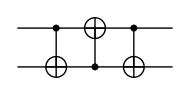

```mathematica
new=QuantumCircuit[CNOT[S[1],S[2]],CNOT[S[2],S[1]],CNOT[S[1],S[2]]]
```

```mathematica
Elaborate[qc-new]
```

0

Let us construct the CZ gate with the √SWAPgate. This is the matrix representation of the the √SWAPgate.

```mathematica
mat=MatrixPower[Matrix@Elaborate@SWAP[S[1],S[2]],1/2];
mat//MatrixForm
```

(1 | 0 | 0 | 0
0 | 1/2+ⅈ/2 | 1/2-ⅈ/2 | 0
0 | 1/2-ⅈ/2 | 1/2+ⅈ/2 | 0
0 | 0 | 0 | 1)

This is an explicit operator expression of the √SWAPgate in terms of the Pauli operators.

```mathematica
sqrtSWAP={ExpressionFor[mat,S@{1,2}],"Label"->"√U"}
```

{(3/4+ⅈ/4)+(1/4-ⅈ/4) S_(,,1)^(,,Z)S_(,,2)^(,,Z)+(1/2-ⅈ/2) S_(,,1)^(,,+)S_(,,2)^(,,-)+(1/2-ⅈ/2) S_(,,1)^(,,-)S_(,,2)^(,,+),Label→√U}

This is a quantum circuit model to construct the CZ gate from the √SWAP gate and single-qubit rotation gates. In this diagram, √U denotes the √SWAPgate and S the quadrant phase gate (or, equivalently, the rotation around the z-axis by angle π/2).

```mathematica
qc=QuantumCircuit[sqrtSWAP,S[1,3],sqrtSWAP,{S[1,7],Dagger@S[2,7]}]
```

-Graphics-

To check if it indeed implements the CZ gate, take a look at the matrix representation of the quantum circuit model.

```mathematica
Matrix[qc]//MatrixForm
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1)

### Controlled-Unitary Gates

Consider a single-qubit rotation acting on the qubit S[2,$]. It is a rotation around the y-axis by angle ϕ.

```mathematica
Let[Real,ϕ]
U=Rotation[ϕ,S[2,2],"Label"->"U"];
U//Elaborate//Matrix//MatrixForm
```

(1/2 ⅇ^(-(ⅈ ϕ)/2)+1/2 ⅇ^((ⅈ ϕ)/2) | -1/2 ⅈ ⅇ^(-(ⅈ ϕ)/2)+1/2 ⅈ ⅇ^((ⅈ ϕ)/2)
1/2 ⅈ ⅇ^(-(ⅈ ϕ)/2)-1/2 ⅈ ⅇ^((ⅈ ϕ)/2) | 1/2 ⅇ^(-(ⅈ ϕ)/2)+1/2 ⅇ^((ⅈ ϕ)/2))

This is a quantum circuit featuring the controlled-unitary gate.

```mathematica
qc=QuantumCircuit[ControlledGate[S[1],U]]
```

-Graphics-

This is the explicit expression of the controlled-U gate operation in terms of the Pauli operators.

```mathematica
op=Elaborate[qc]
```

Cos[ϕ/4]^2+S_(,,1)^(,,Z) Sin[ϕ/4]^2+1/2 ⅈ S_(,,1)^(,,Z)S_(,,2)^(,,Y) Sin[ϕ/2]-1/2 ⅈ S_(,,2)^(,,Y) Sin[ϕ/2]

The controlled-U gate maps the logical basis states as follows.

```mathematica
in=Basis[S@{1,2}];
out=op**in;
Thread[in->out]//TableForm
```

0_(,,S_(,,1))0_(,,S_(,,2))→0_(,,S_(,,1))0_(,,S_(,,2))
0_(,,S_(,,1))1_(,,S_(,,2))→0_(,,S_(,,1))1_(,,S_(,,2))
1_(,,S_(,,1))0_(,,S_(,,2))→Cos[ϕ/2] 1_(,,S_(,,1))0_(,,S_(,,2))+1_(,,S_(,,1))1_(,,S_(,,2)) Sin[ϕ/2]
1_(,,S_(,,1))1_(,,S_(,,2))→Cos[ϕ/2] 1_(,,S_(,,1))1_(,,S_(,,2))-1_(,,S_(,,1))0_(,,S_(,,2)) Sin[ϕ/2]

Let us take a look at the mapping more closely. When the first qubit is set to Ket[0], it does nothing.

```mathematica
Let[Complex,c]
vec=Ket[]c[0]+Ket[S[2]->1]c[2]//KetRegulate[#,S@{1,2}]&
```

c_(,,0) 0_(,,S_(,,1))0_(,,S_(,,2))+c_(,,2) 0_(,,S_(,,1))1_(,,S_(,,2))

```mathematica
new=op**vec
```

c_(,,0) 0_(,,S_(,,1))0_(,,S_(,,2))+c_(,,2) 0_(,,S_(,,1))1_(,,S_(,,2))

When the control qubit -- the first qubit in this case -- is set to 1, it operates the unitary operator on the second qubit.

```mathematica
vec=Ket[S[1]->1]**(Ket[]c[0]+Ket[S[2]->1]c[2])//KetRegulate
```

c_(,,0) 1_(,,S_(,,1))0_(,,S_(,,2))+c_(,,2) 1_(,,S_(,,1))1_(,,S_(,,2))

```mathematica
new=op**vec
```

1_(,,S_(,,1))1_(,,S_(,,2)) (c_(,,2) Cos[ϕ/2]+c_(,,0) Sin[ϕ/2])+1_(,,S_(,,1))0_(,,S_(,,2)) (c_(,,0) Cos[ϕ/2]-c_(,,2) Sin[ϕ/2])

When the control qubit  is in a superposition, the resulting state is an entangled state in general.

```mathematica
vec=Ket[]+Ket[S[1]->1];
KetRegulate[vec,S@{1,2}]
```

0_(,,S_(,,1))0_(,,S_(,,2))+1_(,,S_(,,1))0_(,,S_(,,2))

```mathematica
new=op**vec
```

0_(,,S_(,,1))0_(,,S_(,,2))+Cos[ϕ/2] 1_(,,S_(,,1))0_(,,S_(,,2))+1_(,,S_(,,1))1_(,,S_(,,2)) Sin[ϕ/2]

When the target qubit is set to an eigenstate of the unitary operator, it does not change but the control qubit acquires the phase factor given by the eigenvalue of the target state.

```mathematica
vec=(Ket[]+Ket[S[1]->1])**(Ket[]-I Ket[S[2]->1]);
KetFactor@vec
```

(0_(,,S_(,,1))+1_(,,S_(,,1)))⊗(0_(,,S_(,,2))-ⅈ 1_(,,S_(,,2)))

```mathematica
new=op**vec//TrigToExp;
KetFactor@new
```

(0_(,,S_(,,1))+ⅇ^((ⅈ ϕ)/2) 1_(,,S_(,,1)))⊗(0_(,,S_(,,2))-ⅈ 1_(,,S_(,,2)))

This shows  a quantum circuit model conditionally operating the logic gate U on the target qubit.

```mathematica
$n=3;
cc=Table[CNOT[S[j],S[$n]],{j,1,$n-1}];
op=Rotation[ϕ,S[$n+1,2]];
cU=ControlledGate[S[$n],op];
qc=QuantumCircuit[Sequence@@Flatten@{cc,cU,Reverse@cc}]
```

-Graphics-

This shows how the above quantum circuit model maps the logical basis states. It affects the target qubit only when c_1⊕c_2⊕c_3=1.

```mathematica
ss=S[Range[$n],$];
bs=Basis[S@Range[$n+1]];
out=Elaborate[qc]**bs;
new=KetFactor[#,ss]&/@out;
tbl=Thread[bs->new];
tbl[[;;5]]//TableForm
```

0_(,,S_(,,1))0_(,,S_(,,2))0_(,,S_(,,3))0_(,,S_(,,4))→0_(,,S_(,,1))0_(,,S_(,,2))0_(,,S_(,,3))⊗0_(,,S_(,,4))
0_(,,S_(,,1))0_(,,S_(,,2))0_(,,S_(,,3))1_(,,S_(,,4))→0_(,,S_(,,1))0_(,,S_(,,2))0_(,,S_(,,3))⊗1_(,,S_(,,4))
0_(,,S_(,,1))0_(,,S_(,,2))1_(,,S_(,,3))0_(,,S_(,,4))→0_(,,S_(,,1))0_(,,S_(,,2))1_(,,S_(,,3))⊗(Cos[ϕ/2] 0_(,,S_(,,4))+1_(,,S_(,,4)) Sin[ϕ/2])
0_(,,S_(,,1))0_(,,S_(,,2))1_(,,S_(,,3))1_(,,S_(,,4))→0_(,,S_(,,1))0_(,,S_(,,2))1_(,,S_(,,3))⊗(Cos[ϕ/2] 1_(,,S_(,,4))-0_(,,S_(,,4)) Sin[ϕ/2])
0_(,,S_(,,1))1_(,,S_(,,2))0_(,,S_(,,3))0_(,,S_(,,4))→0_(,,S_(,,1))1_(,,S_(,,2))0_(,,S_(,,3))⊗(Cos[ϕ/2] 0_(,,S_(,,4))+1_(,,S_(,,4)) Sin[ϕ/2])

Consider a controlled-unitary gate.

```mathematica
matU=RandomUnitary[2];
matU//MatrixForm
```

(0.393716+0.0593152 ⅈ | -0.600241+0.693671 ⅈ
0.0565933-0.915569 ⅈ | -0.322771-0.233129 ⅈ)

```mathematica
opU=ExpressionFor[matU,S[2]];
qc1=QuantumCircuit[ControlledGate[S[1],opU,"Label"->"U"]]
```

-Graphics-

For the decomposition, first find the Euler angles of the unitary operator.

```mathematica
detU=Det[matU];
vphi=Arg[detU]/2;
{a,b,c}=TheEulerAngles[matU/Sqrt[detU]]
```

{-1.65859,2.32257,-1.00701}

From the Euler angles, choose the component operators.

```mathematica
opA=EulerRotation[{a,b/2,0},S[2],"Label"->"A"];
opB=EulerRotation[{0,-b/2,-(a+c)/2},S[2],"Label"->"B"];
opC=EulerRotation[{0,0,-(a-c)/2},S[2],"Label"->"C"];
opD=Phase[vphi,S[1,3],"Label"->ϕ];
```

Finally, construct the equivalent quantum circuit model.

```mathematica
qc2=QuantumCircuit[opC,CNOT[S[1],S[2]],opB,CNOT[S[1],S[2]],opA,opD]
```

-Graphics-

Check the result.

```mathematica
Elaborate[qc1-qc2]//Chop
```

0

### General Unitary Gates

Consider a Hermitian operator on a two-qubit system. Physically, it corresponds to a transverse-field Ising model.

```mathematica
H=S[1,1]**S[2,1]+S[1,2]+S[2,2]+S[1,3]+S[2,3]
matH=Matrix[H];
matH//MatrixForm
```

S_(,,1)^(,,X)S_(,,2)^(,,X)+S_(,,1)^(,,Y)+S_(,,1)^(,,Z)+S_(,,2)^(,,Y)+S_(,,2)^(,,Z)

(2 | -ⅈ | -ⅈ | 1
ⅈ | 0 | 1 | -ⅈ
ⅈ | 1 | 0 | -ⅈ
1 | ⅈ | ⅈ | -2)

This is the unitary operator generated by the above Hermitian operator.

```mathematica
U=MultiplyExp[-I  H Pi/4]
```

ⅇ^(-1/4 ⅈ π (S_(,,1)^(,,X)S_(,,2)^(,,X)+S_(,,1)^(,,Y)+S_(,,1)^(,,Z)+S_(,,2)^(,,Y)+S_(,,2)^(,,Z)))

This shows the matrix representation of U in the logical basis.

```mathematica
matU=Matrix[U]//Simplify;
matU//MatrixForm
```

(-(1/2+(5 ⅈ)/6)/(√2) | -(1/6-ⅈ/2)/(√2) | -(1/6-ⅈ/2)/(√2) | (1/2-ⅈ/2)/(√2)
(1/6-ⅈ/2)/(√2) | (1/2+ⅈ/6)/(√2) | -(1/2+(5 ⅈ)/6)/(√2) | -(1/2+ⅈ/2)/(√2)
(1/6-ⅈ/2)/(√2) | -(1/2+(5 ⅈ)/6)/(√2) | (1/2+ⅈ/6)/(√2) | -(1/2+ⅈ/2)/(√2)
(1/2-ⅈ/2)/(√2) | (1/2+ⅈ/2)/(√2) | (1/2+ⅈ/2)/(√2) | -(1/2-ⅈ/2)/(√2))

This shows the decomposition of the unitary matrix into two-level matrices (displaying the first three elements). For the purpose of efficiency, the resulting list is given in terms of TwoLevelU.

```mathematica
twl=GivensFactor[N@matU]//IntegerChop;
twl[[;;4]]
```

{1,GivensRotation[…],GivensRotation[…],GivensRotation[…]}

For a more intuitive form, you can convert TwoLevelU into the normal matrix form using Matrix. Here the first three are shown.

```mathematica
MatrixForm/@Matrix/@twl[[;;3]]
```

{(1 | 0
0 | 1),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 0.188982-0.566947 ⅈ | -0.566947-0.566947 ⅈ
0 | 0 | 0.566947-0.566947 ⅈ | 0.188982+0.566947 ⅈ),(1 | 0 | 0 | 0
0 | -0.162221+0.486664 ⅈ | 0.858395+0. ⅈ | 0
0 | -0.858395+0. ⅈ | -0.162221-0.486664 ⅈ | 0
0 | 0 | 0 | 1)}

Indeed, they reconstruct the original matrix.

```mathematica
new=Dot@@Matrix/@Rest[twl];
matU-new//Chop//MatrixForm
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

Consider a two-level matrix of the form.

```mathematica
matU=ThePauli[6];
code=GivensRotation[matU,{3,4},S@{1,2}];
full=Matrix[code];
full//MatrixForm
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1/(√2) | 1/(√2)
0 | 0 | 1/(√2) | -1/(√2))

It corresponds to a single controlled-unitary gate.

```mathematica
Unfold[code]
```

-Graphics-

Consider a two-level matrix of the form.

```mathematica
matU=ThePauli[6];
code=GivensRotation[matU,{2,4},S@{1,2}];
full=Matrix[code];
full//MatrixForm
```

(1 | 0 | 0 | 0
0 | 1/(√2) | 0 | 1/(√2)
0 | 0 | 1 | 0
0 | 1/(√2) | 0 | -1/(√2))

It corresponds to a single controlled-unitary gate with the control and target qubit exchanged.

```mathematica
Unfold[code]
```

-Graphics-

Consider a two-level matrix of the form.

```mathematica
matU=ThePauli[6];
code=GivensRotation[matU,{2,3},S@{1,2}];
full=Matrix[code];
full//MatrixForm
```

(1 | 0 | 0 | 0
0 | 1/(√2) | 1/(√2) | 0
0 | 1/(√2) | -1/(√2) | 0
0 | 0 | 0 | 1)

In this case, we need to apply the CNOT gate before and after the controlled-unitary gate.

```mathematica
Unfold[code]
```

-Graphics-

Consider a two-level matrix of the form.

```mathematica
matU=ThePauli[6];
code=GivensRotation[matU,{1,4},S@{1,2}];
full=Matrix[code];
full//MatrixForm
```

(1/(√2) | 0 | 0 | 1/(√2)
0 | 1 | 0 | 0
0 | 0 | 1 | 0
1/(√2) | 0 | 0 | -1/(√2))

```mathematica
Unfold[code]
```

-Graphics-

Let us consider again the two-qubit model demonstrated before.

```mathematica
H=S[1,1]**S[2,1]+S[1,2]+S[2,2]+S[1,3]+S[2,3]
U=MultiplyExp[-I  H Pi/4]
```

S_(,,1)^(,,X)S_(,,2)^(,,X)+S_(,,1)^(,,Y)+S_(,,1)^(,,Z)+S_(,,2)^(,,Y)+S_(,,2)^(,,Z)

ⅇ^(-1/4 ⅈ π (S_(,,1)^(,,X)S_(,,2)^(,,X)+S_(,,1)^(,,Y)+S_(,,1)^(,,Z)+S_(,,2)^(,,Y)+S_(,,2)^(,,Z)))

This is the decomposition of matU, the matrix representation of U, into two-level unitary matrices, just showing the first three.

```mathematica
matU=Matrix[U];
twl=GivensFactor[N@matU,S[{1,2},$]]//IntegerChop;
MatrixForm/@Matrix/@twl[[;;3]]
```

{(1 | 0
0 | 1),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 0.188982-0.566947 ⅈ | -0.566947-0.566947 ⅈ
0 | 0 | 0.566947-0.566947 ⅈ | 0.188982+0.566947 ⅈ),(1 | 0 | 0 | 0
0 | -0.162221+0.486664 ⅈ | 0.858395 | 0
0 | -0.858395 | -0.162221-0.486664 ⅈ | 0
0 | 0 | 0 | 1)}

The two-level unitary matrices are rewritten in terms of the CNOT and controlled-unitary gates, again showing the first three. The first element of list twl happens to be the identity matrix in this case, and it is excluded in the further analysis.

```mathematica
gates=Unfold/@Rest[twl];
gates[[;;3]]
```

{-Graphics-,-Graphics-,-Graphics-}

This shows the overall quantum circuit model. Here the same label “U” has been used for different controlled-unitary gates just for convenience. Do not forget to reverse the order before plugging the gates in the quantum circuit model.

```mathematica
qc=QuantumCircuit@@Reverse@Flatten[gates]
```

-Graphics-

Check the above quantum circuit by converting it into the matrix representation.

```mathematica
new=Matrix[qc]//Normal//Simplify;
new//MatrixForm
```

(-0.353553-0.589256 ⅈ | -0.117851+0.353553 ⅈ | -0.117851+0.353553 ⅈ | 0.353553-0.353553 ⅈ
0.117851-0.353553 ⅈ | 0.353553+0.117851 ⅈ | -0.353553-0.589256 ⅈ | -0.353553-0.353553 ⅈ
0.117851-0.353553 ⅈ | -0.353553-0.589256 ⅈ | 0.353553+0.117851 ⅈ | -0.353553-0.353553 ⅈ
0.353553-0.353553 ⅈ | 0.353553+0.353553 ⅈ | 0.353553+0.353553 ⅈ | -0.353553+0.353553 ⅈ)

```mathematica
new-matU//ArrayZeroQ
```

True

## Multi-Control Unitary Gates

This is a three-control unitary gate.

```mathematica
qc=QuantumCircuit[ControlledGate[S@{1,2,3},S[4,1],"Label"->"U"]]
```

-Graphics-

### Gray-Code Method

Consider a three-qubit register as an example.

```mathematica
$L=3;
jj=Range[$L];
cc=S[jj,$];
```

This is the gate to operate on the target qubit.

```mathematica
T=S[$L+1,$];
op=Rotation[Pi/3,T[1]]//Elaborate
```

(√3)/2-1/2 ⅈ S_(,,4)^(,,X)

This decomposes the multi-control unitary gate based on the Gray code -- showing only a part of it. Each component is either CNOT or a two-qubit-control unitary gate.

```mathematica
gc=GrayControlledGate[cc,op]; 
gc[[;;3]]
```

{ControlledGate[{S_(,,1)→1},(2^(1/4) ⅇ^(-(ⅈ π)/24)+2^(1/4) ⅇ^((ⅈ π)/24))/(2 2^(1/4))+((2^(1/4) ⅇ^(-(ⅈ π)/24)-2^(1/4) ⅇ^((ⅈ π)/24)) S_(,,4)^(,,+))/(2 2^(1/4))+((2^(1/4) ⅇ^(-(ⅈ π)/24)-2^(1/4) ⅇ^((ⅈ π)/24)) S_(,,4)^(,,-))/(2 2^(1/4)),Label→V],CNOT[{S_(,,1)→1},{S_(,,2)}],ControlledGate[{S_(,,2)→1},(2^(1/4) ⅇ^(-(ⅈ π)/24)+2^(1/4) ⅇ^((ⅈ π)/24))/(2 2^(1/4))+((-2^(1/4) ⅇ^(-(ⅈ π)/24)+2^(1/4) ⅇ^((ⅈ π)/24)) S_(,,4)^(,,+))/(2 2^(1/4))+((-2^(1/4) ⅇ^(-(ⅈ π)/24)+2^(1/4) ⅇ^((ⅈ π)/24)) S_(,,4)^(,,-))/(2 2^(1/4)),Label→V^†]}

This is a quantum circuit model of the decomposition.

```mathematica
qc=QuantumCircuit@@gc
```

-Graphics-

Finally, check the result. Here, we use the matrix method to evaluate the quantum circuit since it is rather deep.

```mathematica
EchoTiming[expr=ExpressionFor[Matrix@qc,Qubits@qc]];
EchoTiming[new=ControlledGate[cc,op]//Elaborate];
expr-new//Elaborate//Garner//Chop
```

0.730793

0.009964

0

Here, calculating the expression in terms of exact numbers does not have much meaning.

```mathematica
EchoTiming[expr=ExpressionFor[Matrix@N@qc,Qubits@qc]];
EchoTiming[new=ControlledGate[cc,op]//Elaborate];
expr-new//Elaborate//Garner//Chop
```

0.581281

0.009812

0

### Multi-Control NOT Gate

This shows a generalized CNOT gate, controlled by three qubits rather than a single qubit.

```mathematica
qc=QuantumCircuit[CNOT[S@{1,2,3},S[4]]]
```

-Graphics-

Here is the explicit expression of the multi-control NOT gate in terms of the Pauli operators.

```mathematica
op=ExpressionFor[qc]
```

7/8-1/8 S_(,,1)^(,,Z)S_(,,2)^(,,Z)-1/8 S_(,,1)^(,,Z)S_(,,3)^(,,Z)-1/8 S_(,,1)^(,,Z)S_(,,4)^(,,X)-1/8 S_(,,2)^(,,Z)S_(,,3)^(,,Z)-1/8 S_(,,2)^(,,Z)S_(,,4)^(,,X)-1/8 S_(,,3)^(,,Z)S_(,,4)^(,,X)+1/8 S_(,,1)^(,,Z)S_(,,2)^(,,Z)S_(,,3)^(,,Z)+1/8 S_(,,1)^(,,Z)S_(,,2)^(,,Z)S_(,,4)^(,,X)+1/8 S_(,,1)^(,,Z)S_(,,3)^(,,Z)S_(,,4)^(,,X)+1/8 S_(,,2)^(,,Z)S_(,,3)^(,,Z)S_(,,4)^(,,X)-1/8 S_(,,1)^(,,Z)S_(,,2)^(,,Z)S_(,,3)^(,,Z)S_(,,4)^(,,X)+1/8 S_(,,1)^(,,Z)+1/8 S_(,,2)^(,,Z)+1/8 S_(,,3)^(,,Z)+1/8 S_(,,4)^(,,X)

Here we compare it with the expression explicitly constructed in terms of a projection operator.

```mathematica
prj=Multiply@@S[{1,2,3},11];
new=(1-prj)+prj**S[4,1]
op-new//Elaborate
```

1-(11)_(S_(,,1))(11)_(S_(,,2))(11)_(S_(,,3))+(11)_(S_(,,1))(11)_(S_(,,2))(11)_(S_(,,3))S_(,,4)^(,,X)

0

Here we demonstrate a multi-control NOT gate.

```mathematica
$n=4;
$m=2;
cc=Range[$n];
aa=Range[$n+1,$n+$m];
tt=$n+$m+1;
```

```mathematica
qc=QuantumCircuit[CNOT[S[cc],S[tt]],"Visible"->S[aa]]
```

-Graphics-

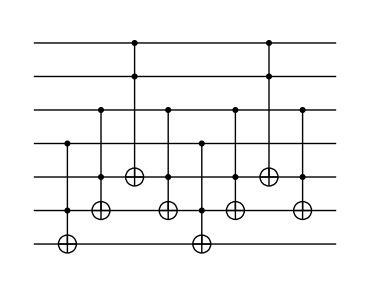

```mathematica
tofa=Table[Toffoli[S[$n-j+1],S[$n+$m-j+1],S[tt-j+1]],{j,1,$m}];
tofb=Toffoli[S[1],S[2],S[$n+1]];
tofc=Rest@tofa;
new=QuantumCircuit[Sequence@@Flatten@{tofa,tofb,Reverse@tofa,tofc,tofb,Reverse@tofc}]
```

```mathematica
EchoTiming[Elaborate[qc-new]]
```

10.963

0

This is a quantum circuit model of the Toffoli gate.

```mathematica
qc=QuantumCircuit[Toffoli[S[1],S[2],S[3]]]
```

-Graphics-

It can be implemented by a combination of two-qubit gates.

```mathematica
gray=GrayControlledGate[S@{1,2},S[3,1]];
new=QuantumCircuit[Sequence@@gray]
```

-Graphics-

```mathematica
qc-new//Elaborate
```

0

Here V=√X, and its matrix representation looks like this.

```mathematica
matV=MatrixPower[ThePauli[1],1/2];
matV*2/(1+I)//MatrixForm
opV=Elaborate@ExpressionFor[matV,S[3]]
```

(1 | -ⅈ
-ⅈ | 1)

(1/2+ⅈ/2)+(1/2-ⅈ/2) S_(,,3)^(,,X)

Reversing the above circuit gives the identical result.

```mathematica
qc=QuantumCircuit@@Reverse@gray
expr=ExpressionFor[qc]
toff-expr
```

-Graphics-

3/4-1/4 S_(,,1)^(,,Z)S_(,,2)^(,,Z)-1/4 S_(,,1)^(,,Z)S_(,,3)^(,,X)-1/4 S_(,,2)^(,,Z)S_(,,3)^(,,X)+1/4 S_(,,1)^(,,Z)S_(,,2)^(,,Z)S_(,,3)^(,,X)+1/4 S_(,,1)^(,,Z)+1/4 S_(,,2)^(,,Z)+1/4 S_(,,3)^(,,X)

-3/4+toff+1/4 S_(,,1)^(,,Z)S_(,,2)^(,,Z)+1/4 S_(,,1)^(,,Z)S_(,,3)^(,,X)+1/4 S_(,,2)^(,,Z)S_(,,3)^(,,X)-1/4 S_(,,1)^(,,Z)S_(,,2)^(,,Z)S_(,,3)^(,,X)-1/4 S_(,,1)^(,,Z)-1/4 S_(,,2)^(,,Z)-1/4 S_(,,3)^(,,X)

This shows another slightly different implementation of the Toffoli gate.

```mathematica
qc=QuantumCircuit@@Permute[gray,Cycles[{{4,3,2,1}}]]
expr=ExpressionFor[qc]
toff-expr
```

-Graphics-

3/4-1/4 S_(,,1)^(,,Z)S_(,,2)^(,,Z)-1/4 S_(,,1)^(,,Z)S_(,,3)^(,,X)-1/4 S_(,,2)^(,,Z)S_(,,3)^(,,X)+1/4 S_(,,1)^(,,Z)S_(,,2)^(,,Z)S_(,,3)^(,,X)+1/4 S_(,,1)^(,,Z)+1/4 S_(,,2)^(,,Z)+1/4 S_(,,3)^(,,X)

-3/4+toff+1/4 S_(,,1)^(,,Z)S_(,,2)^(,,Z)+1/4 S_(,,1)^(,,Z)S_(,,3)^(,,X)+1/4 S_(,,2)^(,,Z)S_(,,3)^(,,X)-1/4 S_(,,1)^(,,Z)S_(,,2)^(,,Z)S_(,,3)^(,,X)-1/4 S_(,,1)^(,,Z)-1/4 S_(,,2)^(,,Z)-1/4 S_(,,3)^(,,X)

This shows the quantum circuit model of the quantum Fredkin gate.

```mathematica
qc=QuantumCircuit[Fredkin[S[1],S@{2,3}]]
```

-Graphics-

This is an explicit operator expression of the Fredkin gate in terms of the Pauli operators.

```mathematica
op=Elaborate[qc]
```

3/4+1/4 S_(,,2)^(,,X)S_(,,3)^(,,X)+1/4 S_(,,2)^(,,Y)S_(,,3)^(,,Y)+1/4 S_(,,2)^(,,Z)S_(,,3)^(,,Z)-1/4 S_(,,1)^(,,Z)S_(,,2)^(,,X)S_(,,3)^(,,X)-1/4 S_(,,1)^(,,Z)S_(,,2)^(,,Y)S_(,,3)^(,,Y)-1/4 S_(,,1)^(,,Z)S_(,,2)^(,,Z)S_(,,3)^(,,Z)+1/4 S_(,,1)^(,,Z)

This is the matrix representation of the Fredkin gate in the logical basis.

```mathematica
mat=Matrix[qc];
mat//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

The Fredkin gate is equivalent to a combination of three Toffoli gates.

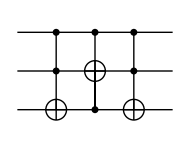

```mathematica
qc2=QuantumCircuit[
Toffoli[S[1],S[2],S[3]],
Toffoli[S[1],S[3],S[2]],
Toffoli[S[1],S[2],S[3]]]
```

```mathematica
op2=Elaborate[qc2]
```

3/4+1/4 S_(,,2)^(,,X)S_(,,3)^(,,X)+1/4 S_(,,2)^(,,Y)S_(,,3)^(,,Y)+1/4 S_(,,2)^(,,Z)S_(,,3)^(,,Z)-1/4 S_(,,1)^(,,Z)S_(,,2)^(,,X)S_(,,3)^(,,X)-1/4 S_(,,1)^(,,Z)S_(,,2)^(,,Y)S_(,,3)^(,,Y)-1/4 S_(,,1)^(,,Z)S_(,,2)^(,,Z)S_(,,3)^(,,Z)+1/4 S_(,,1)^(,,Z)

```mathematica
op-op2
```

0

In fact, the relation between the SWAP gate and the CNOT gate suggests that there is another equivalent quantum circuit model of the Fredkin gate.

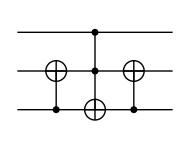

```mathematica
new=QuantumCircuit[
CNOT[S[3],S[2]],
Toffoli[S[1],S[2],S[3]],
CNOT[S[3],S[2]]
]
```

```mathematica
qc-new//Elaborate
```

0

## Universal Quantum Computation

Consider a three-qubit system, and an arbitrary unitary operation on it.

```mathematica
$n=3;
SS=S[Range[$n],$];
mat=RandomUnitary[2^$n];
mat[[;;3,;;3]]//MatrixForm
```

(0.274827+0.32742 ⅈ | -0.232841+0.305784 ⅈ | 0.124906-0.311682 ⅈ
0.361316+0.20392 ⅈ | 0.10806-0.259799 ⅈ | 0.0257501-0.263355 ⅈ
-0.0595-0.358526 ⅈ | 0.216977-0.457289 ⅈ | -0.135113-0.119572 ⅈ)

```mathematica
op=ExpressionFor[mat,SS];
qc=QuantumCircuit[{op,"Label"->"U"}]
```

-Graphics-

```mathematica
twl=GivensFactor[mat];
twl[[3]]//Matrix//Chop//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -0.894298-0.349843 ⅈ | 0.279 | 0
0 | 0 | 0 | 0 | 0 | -0.279 | -0.894298+0.349843 ⅈ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

Let us consider a particular two-level unitary matrix on a three-qubit system. We want to implement it in terms of elementary quantum logic gates.

```mathematica
U=TheRotation[Pi/3,2];
U//MatrixForm
```

((√3)/2 | -1/2
1/2 | (√3)/2)

```mathematica
mat=Matrix@GivensRotation[U,{4,5},2^$n];
mat//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | (√3)/2 | -1/2 | 0 | 0 | 0
0 | 0 | 0 | 1/2 | (√3)/2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
op=ExpressionFor[mat,SS]
```

1/8 (6+√3)+1/8 (2-√3) S_(,,1)^(,,Z)S_(,,2)^(,,Z)+1/8 (2-√3) S_(,,1)^(,,Z)S_(,,3)^(,,Z)+1/8 (-2+√3) S_(,,2)^(,,Z)S_(,,3)^(,,Z)-1/2 S_(,,1)^(,,+)S_(,,2)^(,,-)S_(,,3)^(,,-)+1/2 S_(,,1)^(,,-)S_(,,2)^(,,+)S_(,,3)^(,,+)

Our implementation is based on the Gray code sequence.

```mathematica
gates=Unfold@GivensRotation[U,{4,5},SS]
```

-Graphics-

```mathematica
Matrix[gates]//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | (√3)/2 | -1/2 | 0 | 0 | 0
0 | 0 | 0 | 1/2 | (√3)/2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

## Computational Model of Measurement

First consider a measurement in the logical basis.

```mathematica
Let[Complex,c]
vec=ProductState[S[1]->{c[0],c[1]}];
qc=QuantumCircuit[vec,"Spacer",Measurement@S[1,3],"PortSize"->{2,0.2}]
```

-Graphics-

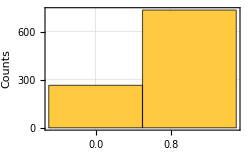

```mathematica
Block[
{c,data},
c[0]=1/2;
c[1]=Sqrt[3]/2;
data=Table[ExpressionFor[qc];Readout@S[1,3],1000];
Histogram[data,FrameLabel->{"Readout","Counts"}]
]
```

Now, consider a measurement in the eigen-basis of the Pauli X operator.

```mathematica
Let[Complex,c]
vec=ProductState[S[1]->{c[0],c[1]}];
qc=QuantumCircuit[vec,S[1,6],Measurement@S[1,3],"PortSize"->{2,0.2}]
```

-Graphics-

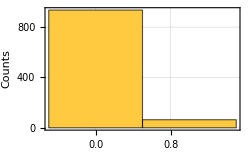

```mathematica
Block[
{c,data},
c[0]=1/2;
c[1]=Sqrt[3]/2;
data=Table[ExpressionFor[qc];Readout@S[1,3],1000];
Histogram[data,FrameLabel->{"Readout","Counts"}]
]
```

This is the "disentangler" quantum circuit, which is the inverse of the entangler quantum circuit .

```mathematica
disentangler=QuantumCircuit[CNOT[S[1],S[2]],S[1,6]]
```

-Graphics-

This shows that the disentangler quantum circuit maps the Bell states into the logical basis states.

```mathematica
op=ExpressionFor[disentangler];
bs=BellState@S@{1,2};
Thread[bs->op**bs]//TableForm
```

(0_(,,S_(,,1))0_(,,S_(,,2))+1_(,,S_(,,1))1_(,,S_(,,2)))/(√2)→0_(,,S_(,,1))0_(,,S_(,,2))
(0_(,,S_(,,1))1_(,,S_(,,2))+1_(,,S_(,,1))0_(,,S_(,,2)))/(√2)→0_(,,S_(,,1))1_(,,S_(,,2))
(0_(,,S_(,,1))1_(,,S_(,,2))-1_(,,S_(,,1))0_(,,S_(,,2)))/(√2)→1_(,,S_(,,1))1_(,,S_(,,2))
(0_(,,S_(,,1))0_(,,S_(,,2))-1_(,,S_(,,1))1_(,,S_(,,2)))/(√2)→1_(,,S_(,,1))0_(,,S_(,,2))

As an example, consider a two-qubit quantum state.

```mathematica
vec=Ket[]+I Ket[S[1]->1]+Ket[S[2]->1]//KetRegulate
```

0_(,,S_(,,1))0_(,,S_(,,2))+0_(,,S_(,,1))1_(,,S_(,,2))+ⅈ 1_(,,S_(,,1))0_(,,S_(,,2))

This is a full quantum circuit model to perform the Bell measurement on the state specified above.

```mathematica
qc=QuantumCircuit[vec,disentangler,Measurement@S[{1,2},3],"PortSize"->{2.6,0.2}]
```

-Graphics-

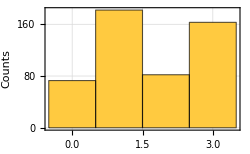

```mathematica
data=Table[ExpressionFor[qc];FromDigits[Readout@S[{1,2},3],2],500];
Histogram[data,FrameLabel->{"Readout","Counts"}]
```